## Tissue-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (11-Nov-2012)) loaded Sun 11 Nov 2012 15:11:30
using xCellerator 0.92 and XSSA 1204002
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

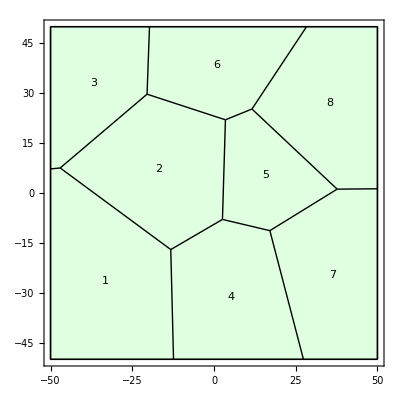

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True, Frame-> True]
```

```mathematica
q
```

Tissue[{{-47.0448,7.52194},{-20.4782,29.7004},{-13.2201,-17.0038},{2.58714,-7.94049},{3.49615,22.0003},{11.6108,25.2403},{17.0873,-11.3159},{37.6677,1.15888},{50,-50},{50,50},{-50,50},{-50,-50},{50.,1.26604},{28.3103,50.},{-19.7295,50.},{-50.,7.24109},{-12.3805,-50.},{27.3575,-50.}},{{1,2},{1,3},{1,16},{2,5},{2,15},{3,4},{3,17},{4,5},{4,7},{5,6},{6,8},{6,14},{7,8},{7,18},{8,13},{9,13},{9,18},{10,13},{10,14},{11,15},{11,16},{12,16},{12,17},{14,15},{17,18}},{{23,7,2,3,22},{1,2,6,8,4},{21,3,1,5,20},{25,14,9,6,7},{8,9,13,11,10},{24,5,4,10,12},{15,13,14,17,16},{19,12,11,15,18}}]